```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

```mathematica
num = Import["test1.txt","Table"]
```

{{1,1,1,1,1,1,1,1,1,1,1},{1,0.999976,1.00002,0.999991,0.999999,1,0.999999,0.999991,1.00002,0.999976,1},{1,1.00002,0.999975,1.00001,1,0.999997,1,1.00001,0.999975,1.00002,1},{1,0.999991,1.00001,0.999997,1,1,1,0.999997,1.00001,0.999991,1},{1,0.999999,1,1,1,1,1,1,1,0.999999,1},{1,1,0.999999,1,1,1,1,1,0.999999,1,1},{1,1,0.999999,1,1,1,1,1,0.999999,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,0.999998,1,0.999999,1,1,1,0.999999,1,0.999998,1},{1,1,0.999998,1,1,1,1,1,0.999998,1,1},{1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
true = Table[1,{i,0,1/0.1},{j,0,1/0.1}]
```

{{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}}

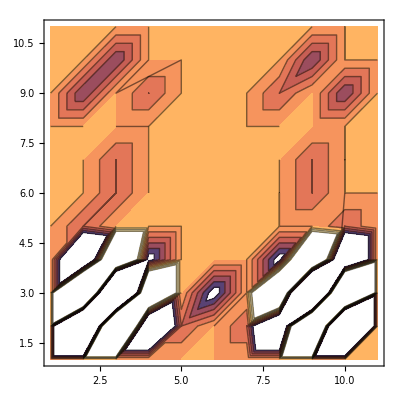

```mathematica
ListContourPlot[num-true]
```

```mathematica
g = Show[ListPlot3D[num,PlotRange->{{1,10},{1,10},{0.95,1.05}},PlotLegends->{{ "Численное решение"}}],ListPlot3D[true,PlotStyle->Blue,PlotLegends->{{ "Истинное решение"}}],ImageSize->600]
```

-Graphics3D-

```mathematica
Export["test1.png",g]
```

test1.png